```mathematica
myAxesSize=21;
myLabelSize=18;
myImageSize=1000;
SetDirectory[NotebookDirectory[]];
```

## Code Output

```mathematica
h={1,1/2,1/4,1/8,1/16};
Errors1={0,0,0.485574,532.662,0.00245532,0.0372678,0.897188,65.8037};
Errors2={0,0,0.0647443,524.115,0.000607743,0.0372678,0.111753,57.387};
Errors3={0,0,0.00871085,521.967,0.000148749,0.0372678,0.0151314,55.0692};
Err={Errors1,Errors2,Errors3};
```

## Getting conv vectors

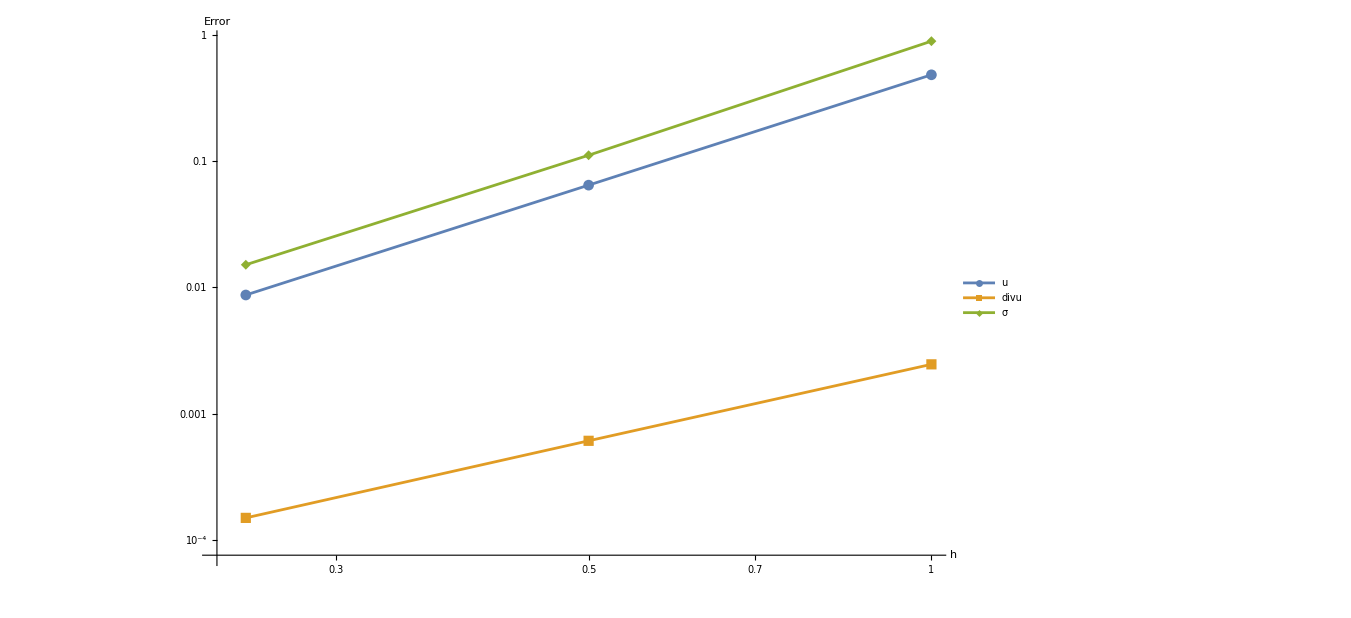

```mathematica
uerr=Table[{h[[i]],Err[[i,3]]},{i,Length[Err]}];
divuerr=Table[{h[[i]],Err[[i,5]]},{i,Length[Err]}];
sigmaerr=Table[{h[[i]],Err[[i,7]]},{i,Length[Err]}];
ListLogLogPlot[{uerr,divuerr,sigmaerr},Joined->True,PlotMarkers->Automatic,ImageSize->myImageSize,AxesLabel->{Style["h",myAxesSize,Black],Style["Error",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*1.2,Bold,Black],PlotLegends->Placed[LineLegend[{"u","divu","σ"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.75}],GridLines->Automatic]
```

## Taxa

```mathematica
Table[Log[uerr[[i,2]]/uerr[[i+1,2]]]/Log[2],{i,1,Length[uerr]-1}]
Table[Log[divuerr[[i]]/divuerr[[i+1]]]/Log[2],{i,1,Length[divuerr]-1}]
Table[Log[sigmaerr[[i]]/sigmaerr[[i+1]]]/Log[2],{i,1,Length[sigmaerr]-1}]
```

{2.90687,2.89387}

{{1,2.01438},{1,2.03058}}

{{1,3.0051},{1,2.8847}}